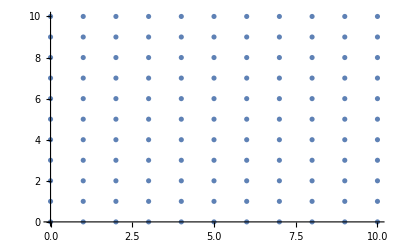

```mathematica
side=10;
points=Flatten[Table[{x,y},{x,0,side},{y,0,side}],1];
ListPlot[points]
```

```mathematica
Manipulate[
shift=((margin-1)*side)/2;
transform[{x_,y_}]:={
x*margin-shift,
y*margin-shift
};
ListLinePlot[{points,transform/@points}//Transpose,PlotRange->Full,Mesh->Full],
{margin,0.5,1.5}]
```